## Zestaw 8

Katarzyna Sowa

## 3N

Metoda Romberga przyblizono calke ∫_0^∞ Sin((1+√x)/(1+x^2))ⅆx.

```mathematica
f[x_]:=Sin[(1+√x)/(1+x √2)] ⅇ^-x;
```

```mathematica
Romberg[a_,b_,prec_]:=Module[{},
reg[x_]:=Module[{k},
R_⟦x+1,1⟧=R_⟦x,1⟧/2+h/2∑_(k=1)^m f[a+h/2 (2 k-1)]; 
m=2 m;]; 
h=b-a; 
m=1; 
j=1; 
 R={{0}};
R_⟦1,1⟧ = h/2(f[a] + f[b]); 
Print[ R_⟦j⟧ ]; 
While[j≤11 && prec<1, j++; 
R = Append[ R,Table[0,{j}] ]; 
reg[j-1];
For[ k=1, k≤j-1, k++,
R_⟦j,k+1⟧=R_⟦j,k⟧+(R_⟦j,k⟧-R_⟦j-1,k⟧)/(4^k-1); ]  ]; 
Return[ Print["Przyblizona wartosc calki wynosi: ",R_⟦j,j⟧]]; ];
```

```mathematica
Romberg[0.0,100,0.00000001];
```

{42.0735}

Przyblizona wartosc calki wynosi: 0.0125142

## 4N

Calke mozna interpretowac jako pole powierzchni pod wykresem funkcji podcalkowej.

```mathematica
f[t_]:=Cos[(1+t)/(t^2+0.04)] ⅇ^(-t^2);
```

```mathematica
Needs["Graphics`FilledPlot`"];
```

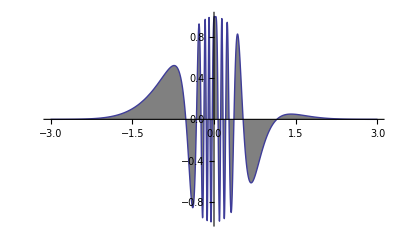

```mathematica
FilledPlot[f[t],{t,-3,3},PlotRange->Full]
```

Obliczanie granicy lim_(x→∞) F(x)=∫_(-∞)^x Cos[(1+t)/(t^2+0.04)]ⅇ^(-t^2)ⅆt

```mathematica
Simpson[aa_,bb_,m_]:=
Module[{a=N[aa],mm=m,b=N[bb],k,,X},
mm=2;
h = (b-a)/(2m); 
Subscript[X, k_] = a + k h; 
Return[ h/6(f[a]+f[b]+2∑_(k=1)^(m-1) f[Subscript[X, 2k]]+4∑_(k=1)^m f[Subscript[X, 2k-1]]) ]; ];
```

```mathematica
ka[a_,b_,err_]:=Module[{c},
c=(a+b)/2; 
ab=Simpson[a,b,err]; 
ac=Simpson[a,c,err]; 
cb=Simpson[c,b,err]; 
If[ Abs[ab-ac-cb]<err,
Return[ ac+cb ],
Return[ka[a,c,err/2]]]; ]
 
Print["Wynik: Lim_(x → ∞)F(x)=", ka[-10,10.0,0.00000001]];
```

Wynik: Lim_(x → ∞)F(x)=3.08214×10^-17